# Numerical Integration of the Invertase Reaction

#### G. Woehlke, 2018 - Nov. 2025

## Numerical integration with NDSolve for analysis of the full, reversible invertase reaction

```mathematica
Unset[{k12,k21,k23,k32}]
```

{Null,Null,Null,Null}

```mathematica
CellPrint[TextCell["Reaction Scheme",CellTags->"MMScheme","Subsection"]]
```

### Reaction Scheme

The reaction scheme is the following (E - enzyme, S - sucrose (or ‘Saccharose’ or substrate), ES - enzyme-substrate complex, G - glucose, F - fructose):
     -Graphics-

In contrast to the standard textbook system, in which substrate binding is equilibrated infinitely fast (and consequently treaded as a simple dissociation constant, K_S), and with a single product release step, the real invertase reaction is much more complicated and involves two (reversible!) product release steps. The system is described by the following set of equations, derived from its partial reactions r_i:

```mathematica
r1=k12 cE[t]cS[t];
r2=k21 cES[t];
r3=k23 cES[t];
r4=k32 cEG[t]cF[t] ;
r5=k35 cEG[t];
r6=k53 cE[t]cG[t];
r7=k24 cES[t];
r8=k42 cEF[t]cG[t];
r9=k45 cEF[t];
r10=k54 cE[t]cF[t];
```

The biochemical system requires that glucose and fuctose are always present at the same concentrations:

```mathematica
eqEqn={(*cG[t]==cS[0]-cS[t]+cG[0],*)
cE[t]+cES[t]+cEG[t]+cEF[t]==(*0.1*)cE[0](*,cF[t]==cS[0]-cS[t]+cF[0]*)(*cG[t]==(*5.*)cS[0]-cS[t]*)}
```

{cE[t]+cEF[t]+cEG[t]+cES[t]==cE[0]}

We ask ourselves how quickly the concentrations of all reaction partners and intermediates change, and set up a system the followoing equations:

```mathematica
Unset[{t}];(* In case defined elsewhere *)
```

```mathematica
eqnsFulMM={
D[cE[t],t]==-r1 +r2+r5-r6+r9-r10,
D[cES[t],t]==r1-r2-r3+r4-r7+r8,
D[cEG[t],t]==r3-r4-r5+r6 ,
D[cEF[t],t]==r7-r8-r9+r10 ,
D[cS[t],t]==-r1+r2,
D[cG[t],t]==+r5-r6+r7-r8, 
D[cF[t],t]==+r3-r4+r9-r10(*,
cE[t]+cES[t]+cEG[t]+cEF[t]==(*0.1*)cE[0]*)
};
```

```mathematica
eqnsFulMM//TableForm
```

cE'[t]==k45 cEF[t]+k35 cEG[t]+k21 cES[t]-k54 cE[t] cF[t]-k53 cE[t] cG[t]-k12 cE[t] cS[t]
cES'[t]==-k21 cES[t]-k23 cES[t]-k24 cES[t]+k32 cEG[t] cF[t]+k42 cEF[t] cG[t]+k12 cE[t] cS[t]
cEG'[t]==-k35 cEG[t]+k23 cES[t]-k32 cEG[t] cF[t]+k53 cE[t] cG[t]
cEF'[t]==-k45 cEF[t]+k24 cES[t]+k54 cE[t] cF[t]-k42 cEF[t] cG[t]
cS'[t]==k21 cES[t]-k12 cE[t] cS[t]
cG'[t]==k35 cEG[t]+k24 cES[t]-k53 cE[t] cG[t]-k42 cEF[t] cG[t]
cF'[t]==k45 cEF[t]+k23 cES[t]-k54 cE[t] cF[t]-k32 cEG[t] cF[t]

For this rather complex system, the analytical solution does not work...

```mathematica
DSolve[{eqnsFulMM,ic},{cE[t],cES[t],cEG[t],cEF[t],cS[t],cG[t],cF[t]},t];
```

...but the numerical integration does. Set the rate constants:

```mathematica
CellPrint[TextCell["Parameters",CellTags->"params","Subsection"]]
```

### Parameters

```mathematica
params={k12->2.,k21->0.5,k23->10.0,k32->0.25,k35->5.0,k53->5.0,k24->10.0,k42->2.5,k45->5.0,k54->5.0};
```

Choose how long to observe:

```mathematica
tEnd=20.;
```

Perform the numerical integration with the indicated initial concentrations:

```mathematica
solFullSystem=NDSolve[{
(*equations: *)
{D[cE[t],t]==-r1 +r2+r5-r6+r9-r10,
D[cES[t],t]==r1-r2-r3+r4-r7+r8,
D[cEG[t],t]==r3-r4-r5+r6 ,
D[cEF[t],t]==r7-r8-r9+r10 ,
D[cS[t],t]==-r1+r2,
D[cG[t],t]==+r5-r6+r7-r8, 
D[cF[t],t]==+r3-r4+r9-r10,
(*init: *)
cE[0]==0.1,
cES[0]==0.,
cEG[0]==0.,
cEF[0]==0.,
cS[0]==2.9,
cG[0]==0.0,
cF[0]==0.1}}
/.params,
(*functions: *){cE,cES,cEG,cEF,cS,cG,cF},
{t,0,tEnd}]
```

{{cE→InterpolatingFunction[…],cES→InterpolatingFunction[…],cEG→InterpolatingFunction[…],cEF→InterpolatingFunction[…],cS→InterpolatingFunction[…],cG→InterpolatingFunction[…],cF→InterpolatingFunction[…]}}

```mathematica
Manipulate[Plot[Evaluate[{cE[t],cES[t],cEG[t],cEF[t],cS[t],cG[t],cF[t]}/.solFullSystem],{t,0,tEnd},
PlotRange->{{0,xaxis},Full},PlotStyle->{{Blue,Thickness[thn]},{Darker[Blue],Thickness[thn]},{Green,Thickness[thn]},{Darker[Green],Thickness[thn]},{Lighter[Green],Thickness[thn]}},
ImageSize->is,
Epilog->{
Inset[Style[
"ES complex",fs,Bold,Darker[Green]],Scaled[{.9,.12}]],
Inset[Style[
"Sucrose",fs,Bold,Darker[Green]],Scaled[{.1,.6}]],
Inset[Style[
"Fructose,\rGlucose",fs,Bold,Blue],Scaled[{.1,.4}]],
Inset[Style[
StringJoin["k_12= ",ToString[params[[1,2]]]," M^-1s^-1","\nk_21 = ",ToString[params[[2,2]]]," s^-1",
"\nk_23 = ",ToString[params[[3,2]]]," s^-1","\nk_32 = ",ToString[params[[4,2]]]," M^-1s^-1",
"\nk_35 = ",ToString[params[[5,2]]]," s^-1","\nk_53 = ",ToString[params[[6,2]]]," M^-1s^-1",
"\nk_24 = ",ToString[params[[7,2]]]," s^-1","\nk_42 = ",ToString[params[[8,2]]]," M^-1s^-1",
"\nk_45 = ",ToString[params[[9,2]]]," s^-1","\nk_54 = ",ToString[params[[10,2]]]," M^-1s^-1"],12(*fs*),Black,TextAlignment->Left],Scaled[{.85,.75}]]
},
PlotRange->{{-.05,tEnd},Automatic},
AxesLabel->{"time","concentration"},
LabelStyle->Directive[FontFamily->Arial,Bold,fs]],
{{is,720,"Image Size"},{450,650,720,950,1050,1280}},
{{thn,0.005,"Line Thickness"},{0.002,0.0035,0.005,0.0067,0.008,0.01}},
{{fs,14,"Font Size"},{9,12,14,18,24}},
{{xaxis,tEnd},0.2,tEnd,0.1(*,Appearance->"Open"*)}]
```

ReplaceAll::reps: {solFullSystem} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification params⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification params⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification params⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {solFullSystem} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {solFullSystem} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification params⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification params⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification params⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {solFullSystem} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Button["Go to reaction scheme",NotebookLocate[{"MathCode_07_MichaelisMenten_ExtendedSystem.nb","MMScheme"}],Background->LightYellow]
```

Go to reaction scheme

Temporal change of substrate (sucrose, orange) and product concentrations (either glucose or fructose, present at equal concentrations, violet).

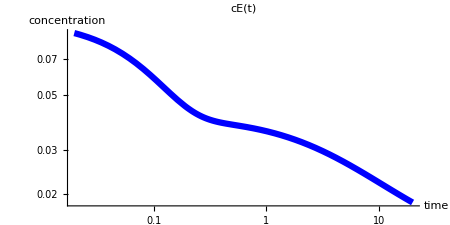
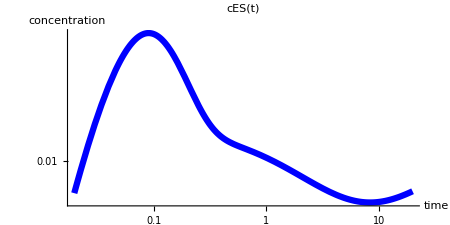
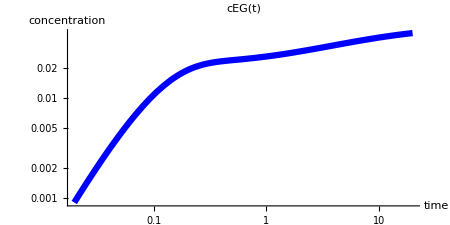
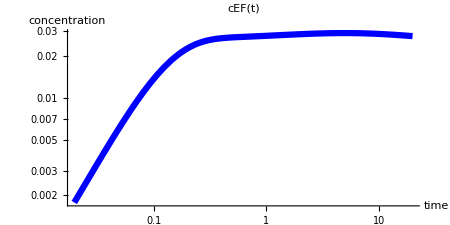
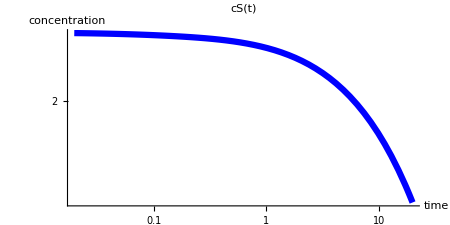
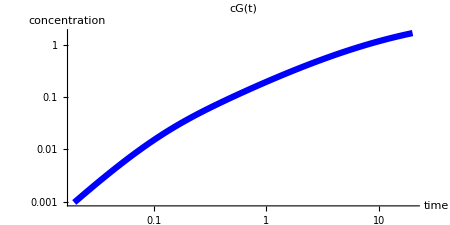
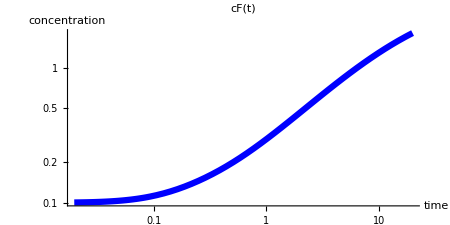

```mathematica
LogLogPlot[Evaluate[#[t]/.solFullSystem],{t,0,tEnd}, PlotRange->{{-0.05,tEnd},{0,Automatic}},
PlotLabel->#[t],
PlotStyle->{{Blue,Thickness[0.01]}},
AxesLabel->{"time","concentration"},
LabelStyle->Directive[FontFamily->Arial,Bold,14],
AspectRatio->0.5,ImageSize->450]& /@ {cE,cES,cEG,cEF,cS,cG,cF}
```

Legend: Temporal change of the concentrations of all seven components involved.

```mathematica
Button["Enter new parameters",NotebookLocate[{"MathCode_07_MichaelisMenten_ExtendedSystem.nb","params"}],Background->LightYellow]
```

Enter new parameters

1. Evaluate the dependence of the reaction velocity (as defined by the rate at which product occurs) on the substrate dependence (e.g. by setting in different substrate concentrations and graphical analysis of the c_glucose[t] graph)!